```mathematica
A=-Ω^2+Δ^2+δ^2;
B=2*Δ*δ;
Λ=-2(δ^2/(A √(1-(B/A)^2))-(A/(4*δ^2)-1)(1-1/(√(1-(B/A)^2))));(*Subscript[π, 22]*)
Ξ=-2(1+Ω^2/(A √(1-(B/A)^2)));(*Subscript[π, 33]*)
Φ=(ⅈ*Ω)/δ(1+(2*δ^2-A)/(A √(1-(B/A)^2)));(*Subscript[π, 23]*)
Ψ=-(ⅈ*Ω)/δ(1+(2*δ^2-A)/(A √(1-(B/A)^2)));(*Subscript[π, 32]*)
ψ=-2((A-A √(1-(B/A)^2))/(2δ)^2); (*Subscript[π, 11]*)
```

```mathematica
Δ=4*0.5;(*Rashba Spin Orbit Coupling*)
u=.3;(*Coulomb energy time density of states*)
δ=(2*α)/(1-u);(*Renormalized zeeman energy. Here α is α/Subscript[ϵ, F]*)
```

```mathematica
f1[α_]:=1+u/2(Λ+Ξ+u/2(Λ*Ξ-Φ*Ψ))(*Mode equation arising from Subscript[π, 22],Subscript[π, 33],Subscript[π, 23],Subscript[π, 32] *)
g1[α_]:=Ω^2-(Δ+δ)^2(*Particle hole excitation spectrum *)
g2[α_]:=Ω^2-(Δ-δ)^2(*Particle hole excitation spectrum *)
h[α_]:=1+u/2 ψ;(*Mode equation arising from Subscript[π, 11]*)
```

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, #1 > Re[√(Times[« 4 »] + Times[« 2 »])^2] &].

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0.36719757717293205`  + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + « 1 » encountered.

∞::indet: Indeterminate expression 0.3941117755655752`  + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + « 1 » encountered.

∞::indet: Indeterminate expression 0.5301655516300043`  + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + « 1 » encountered.

General::stop: Further output of indet will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, #1 > Re[√(Times[« 4 »] + Times[« 2 »])^2] &].

General::stop: Further output of Select will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, 0 < #1 < Re[√(Δ + Times[« 2 »])^2] &].

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0.36719757717293205`  + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + « 1 » encountered.

∞::indet: Indeterminate expression 0.3941117755655752`  + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + « 1 » encountered.

∞::indet: Indeterminate expression 0.5301655516300043`  + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + « 1 » encountered.

General::stop: Further output of indet will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, 0.` < #1 < Re[√(Δ + Times[« 2 »])^2] &].

General::stop: Further output of Select will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, Positive].

General::stop: Further output of Select will be suppressed during this calculation.

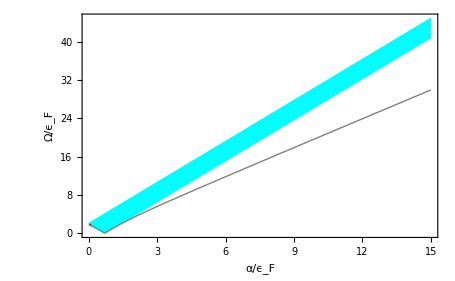

```mathematica
L1=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Max@Select[w,#>Re[√(((2(2-u)δ)/u-δ)^2)]&]},{α,.01,15,0.001}],PlotStyle->Green];
L11=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Min@Select[w,0<#<Re[√((Δ-δ)^2)]&]},{α,.01,15,0.001}],PlotStyle->Gray];
L3=ListLinePlot[Table[ {α,w=Ω/.NSolve[h[α]==0 ,Ω];Min@Select[w,Positive]},{α,.01,15,0.001}],PlotStyle->Red];
L4=Plot[{(Δ+δ),Abs[(Δ-δ)]},{α,.01,15},PlotStyle->{Cyan,Cyan,Cyan},Filling->1->{2},FillingStyle->Cyan,Frame->True,FrameLabel->{α/Subscript[ϵ, F],Ω/Subscript[ϵ, F]}];
(*ListLinePlot[Table[ {α,w=Ω/.NSolve[h[α]==0 ,Ω];Min@Select[w,Positive]},{α,0.01,.5,0.005}]]*)
Show[L4,L1,L11,L3]
```

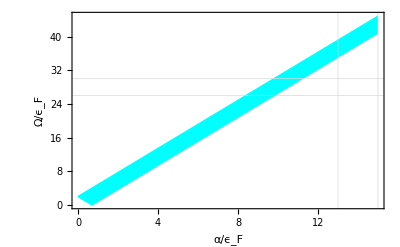

```mathematica
L4=Plot[{(Δ+δ),Abs[(Δ-δ)]},{α,.001,15},PlotStyle->{Cyan,Cyan,Cyan},Filling->1->{2},FillingStyle->Cyan,Frame->True,GridLines->{{13,15},{26,30}},FrameLabel->{α/Subscript[ϵ, F],Ω/Subscript[ϵ, F]},FrameTicks->{{Automatic,{26,30}},{Automatic,{13,15}}}]
```

```mathematica
L11=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Min@Select[w,0<#<Re[√((Δ-δ)^2)]&]},{α,0.65,.75,0.001}],PlotStyle->Gray];
```

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, 0 < #1 < Re[√(Δ + Times[« 2 »])^2] &].

Select::normal: Nonatomic expression expected at position 1 in Select[Ω, 0.` < #1 < Re[√(Δ + Times[« 2 »])^2] &].

General::stop: Further output of Select will be suppressed during this calculation.

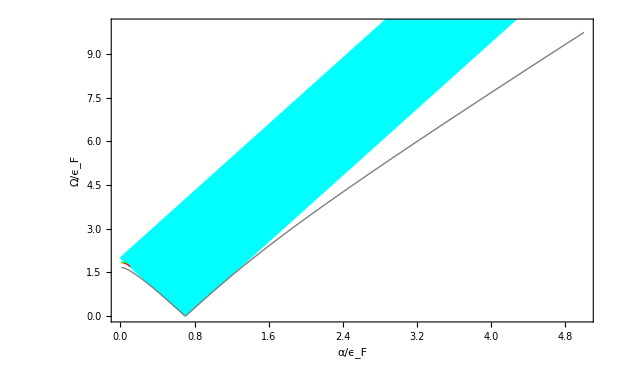

```mathematica
Show[L4,L11,L3,L1,PlotRange-> {{0.001,5},{0,10}}]
```

```mathematica
PlotExplorer
```

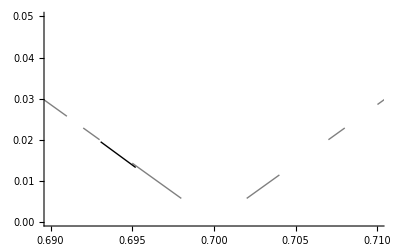

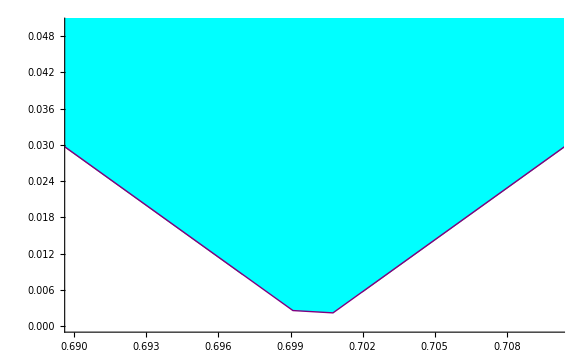

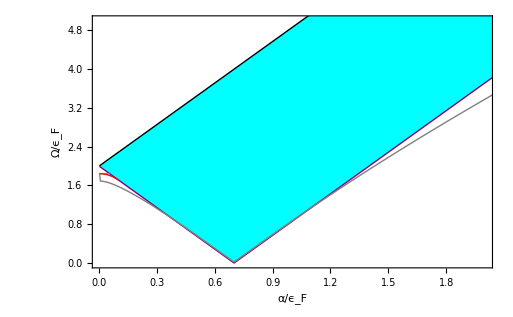

```mathematica
(*Magnified view of splited collective modes behavior.*)
```

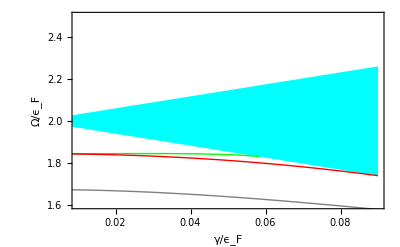

```mathematica
L1=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Max@Select[w,#>Re[√(((2(2-u)δ)/u-δ)^2)]&]},{α,0.002,.09,0.0005}],PlotStyle->Green];
L11=ListLinePlot[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Min@Select[w,0<#<Re[√((Δ-δ)^2)]&]},{α,0.002,.09,0.0005}],PlotStyle->Gray];
L3=ListLinePlot[Table[ {α,w=Ω/.NSolve[h[α]==0 ,Ω];Min@Select[w,Positive]},{α,0.002,.09,0.0005}],PlotStyle->Red];
L4=Plot[{(Δ+δ),Abs[(Δ-δ)]},{α,.002,.09},PlotStyle->{Cyan,Cyan,Cyan},Filling->1->{2},FillingStyle->Cyan,Frame->True,FrameLabel->{γ/Subscript[ϵ, F],Ω/Subscript[ϵ, F]}];
(*ListLinePlot[Table[ {α,w=Ω/.NSolve[h[α]==0 ,Ω];Min@Select[w,Positive]},{α,0.01,.5,0.005}]]*)
Show[L4,L1,L11,L3,PlotRange->{{0.01,0.09},{1.6,2.5}},AxesOrigin->{0,0}]
```

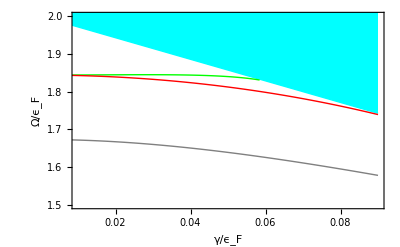

```mathematica
Show[L4,L1,L3,L11,PlotRange->{{0.01,0.09},{1.5,2}},AxesOrigin->{0,0}]
```

```mathematica
Show[L11,L4,L1,L3,PlotRange->{{.001,.23},{0.15,3}},AxesOrigin->{.0008,0.08},Frame->True,FrameLabel->{Style["γ/ϵ_F",Small,Bold,Black],Style[" Ω/ϵ_F" ,Small,Bold,Black]}]
```

```mathematica
GridLines->{Automatic},
```

```mathematica
Show[L4,L1,L11,L3,PlotRange->{{.001,15},{0,35}},Frame-> True,FrameLabel->{Style["γ/ϵ_F",Small,Bold,Black],Style[" Ω/ϵ_F" ,Small,Bold,Black]},Epilog->{Darker[Red],Line[{{0,32.5},{1,32.5}}],Text[" Ω_11/ϵ_F",{2,32.5}],Darker[Green],Line[{{0,28.5},{1,28.5}}],Text["Ω^+/ϵ_F  ",{2,28.5}],
Darker[Gray],Line[{{0,23.5},{1,23.5}}],Text[" Ω^-/ϵ_F ",{2,23.5}]}, ImageSize->Scaled[0.75]]
```

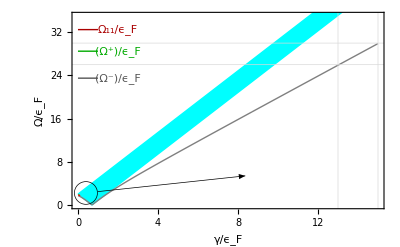

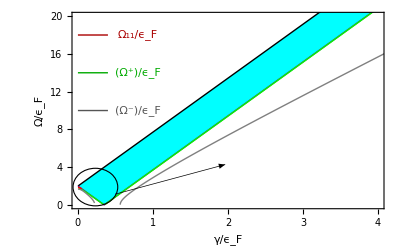

Less::nord: Invalid comparison with 0.5036566010824962`  + 0.0005431615039562277` ⅈ attempted.

General::stop: Further output of Less will be suppressed during this calculation.

0.01 | 0.449417
0.11 | 0.320527
0.21 | 0.176082
0.31 | 0.0230758
0.41 | 0.13065

0.01 | {0.736923,-0.736923,0.503657+0.000543162 ⅈ,0.503657-0.000543162 ⅈ,-0.503657+0.000543161 ⅈ,-0.503657-0.000543161 ⅈ,-0.449417,0.449417,0.40208,-0.40208}
0.11 | {0.812138,-0.812138,0.745751,-0.745751,-0.671966,0.671966,0.320527,-0.320527,-0.280544,0.280544}
0.21 | {1.07403+0.00771413 ⅈ,1.07403-0.00771413 ⅈ,-1.07403+0.00771413 ⅈ,-1.07403-0.00771413 ⅈ,-0.176082,0.176082,0.+0.0914727 ⅈ,0.-0.0914727 ⅈ}
0.31 | {1.58253,-1.58253,1.21755,-1.21755,0.+0.233097 ⅈ,0.-0.233097 ⅈ,-0.0230758,0.0230758}
0.41 | {2.06033,-2.06033,-1.41826,1.41826,0.+0.245498 ⅈ,0.-0.245498 ⅈ,-0.13065,0.13065}

0.01 | {0.484615}
0.11 | {0.330769}
0.21 | {0.176923}
0.31 | {0.0230769}
0.41 | {0.130769}

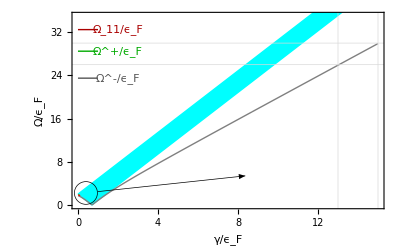

```mathematica
Grid[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω]; Max@Select[w,0<#<√((Δ-δ)^2)&]},{α,0.01,0.5,0.1}]]
Grid[Table[ {α,w=Ω/.NSolve[f1[α]==0 ,Ω] },{α,0.01,0.5,0.1}]]
Grid[Table[ {α,w=Ω/.NSolve[(Δ-δ)^2==Ω^2 ,Ω];Sort@Select[w,Positive]},{α,0.01,0.5,0.1}]]
```